## Summary of results : Ammonia and Acetic Acid

```mathematica
scl=5/246
```

5/246

6M : Inert

```mathematica
ntotal=10
```

10

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Inert\\5%\\6M\\"
SetDirectory[dir1];
```

C:\Users\mariana\Desktop\LastPictures\Inert\5%\6M\

```mathematica
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataInRGB6M.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


(*If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];*)

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tGreenAll0=Max[mtGreenAll];
tRedAll0=Max[mtRedAll];
tBlueAll0=Max[mtBlueAll];

scmtGreenAll=mtGreenAll/tGreenAll0;
scmtRedAll=mtRedAll/tRedAll0;
scmtBlueAll=mtBlueAll/tBlueAll0;

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]]
```

{1.19405,0.953988,0.831777,0.641898,0.513362,0.497874,0.578712,0.442626,0.398715,0.473015,0.448641,0.418015,0.391452,0.440034,0.437838,0.458993,0.465059,0.472544,0.445834,0.421961,0.371178,0.3253,0.269592,0.210112,0.179318,0.190276,0.229398,0.25771,0.291433,0.304173,0.31505,0.323233,0.341204,0.360419,0.384326}

```mathematica
Needs["ErrorBarPlots`"]
```

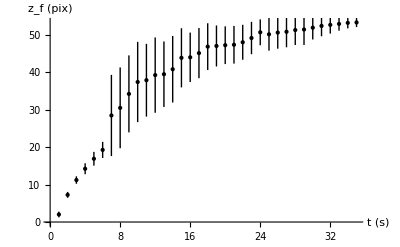
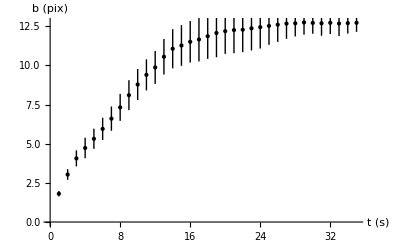
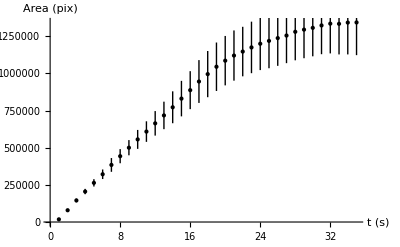
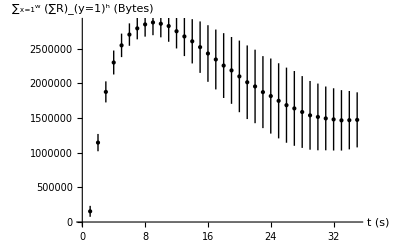
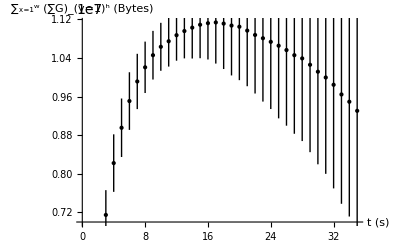
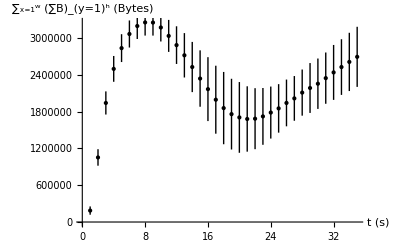
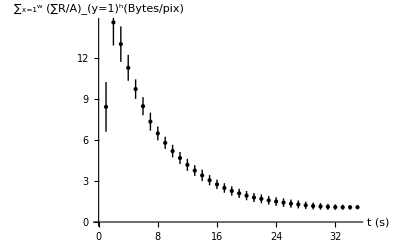
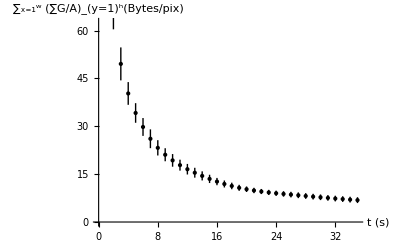

```mathematica
PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionAAI6, radiustAAI6, areaAAI6, redAAI6, greenAAI6, blueAAI6,cRedAAI6,cGreenAAI6,cBlueAAI6}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Black],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black],ErrorListPlot[PlotDatacBlue,AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Black]}
```

```mathematica
{ redAAI6CC, greenAAI6CC, blueAAI6CC,cRedAAI6CC,cGreenAAI6CC,cBlueAAI6CC}=
{ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Red],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Green],ErrorListPlot[PlotDatacBlue,AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->Blue]}
```

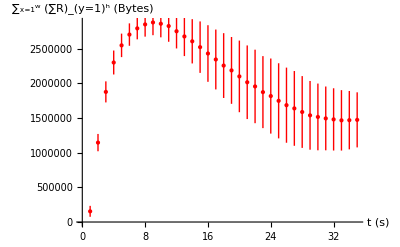
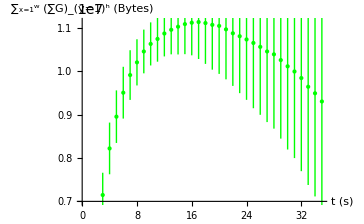
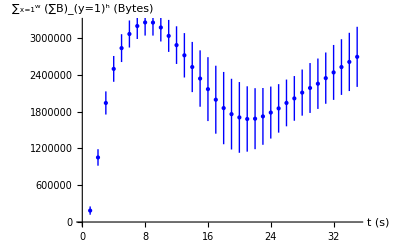
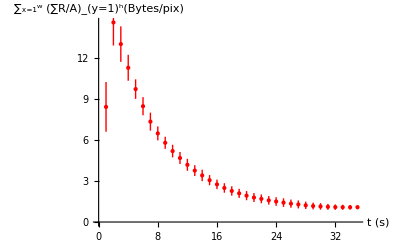
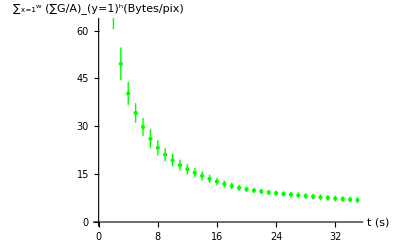
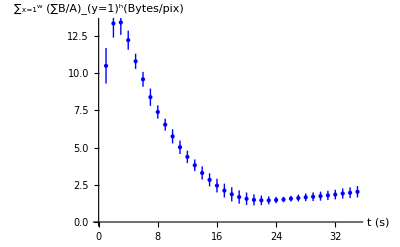

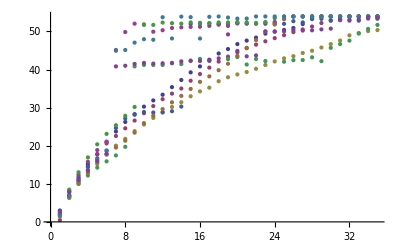
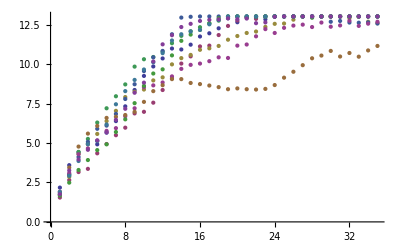

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

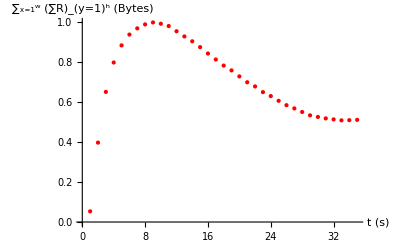
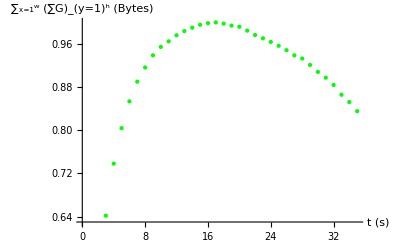
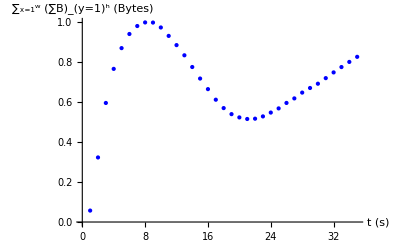

```mathematica
{ sclred, sclgreen, sclblue}=
{ErrorListPlot[scmtRedAll, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[scmtGreenAll, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[scmtBlueAll, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```

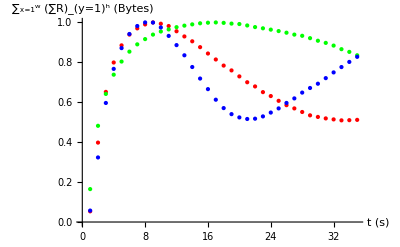

```mathematica
Show[sclred, sclgreen, sclblue]
```

6M : Reactive

```mathematica
ntotal=10
```

10

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\6M\

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_4\MB_4_AscA~0.05M\

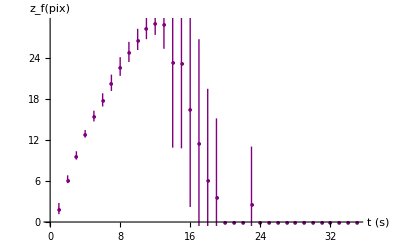
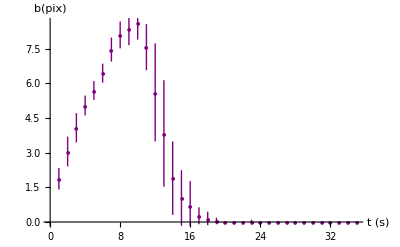
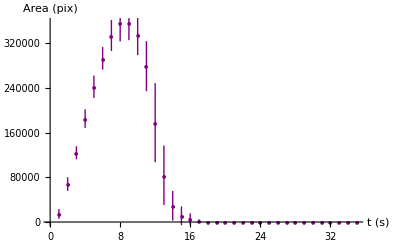
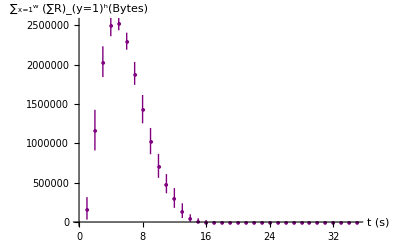
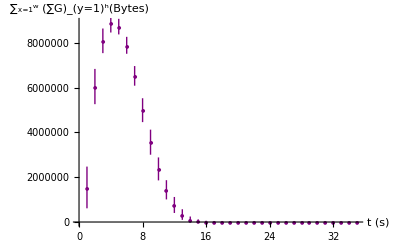
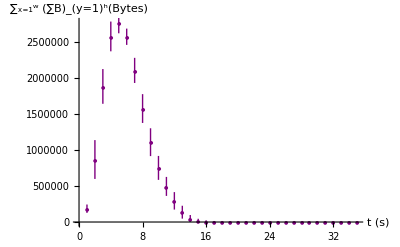
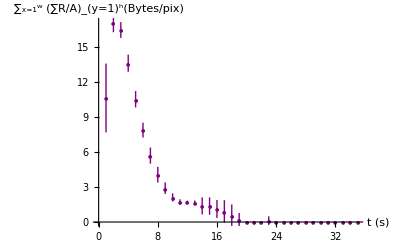
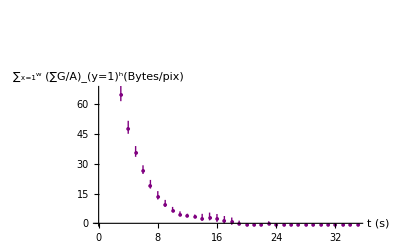

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\6M\\"
SetDirectory[dir1];
"C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_4\\MB_4_AscA~0.05M\\"
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGB6M.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tGreenAll6=Max[mtGreenAll];
sclmtGreenAll6=mtGreenAll[[4;;35]]/tGreenAll6;

tGreenAll6=Max[mtGreenAll];
ssclmtGreenAll6=mtGreenAll/tGreenAll6;

tRedAll6=Max[mtRedAll];
ssclmtRedAll6=mtRedAll/tRedAll6;

tBlueAll6=Max[mtBlueAll];
ssclmtBlueAll6=mtBlueAll/tBlueAll6;

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]];

PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionAAR6, radiustAAR6, areaAAR6, redAAR6, greenAAR6, blueAAR6,cRedAAR6,cGreenAAR6,cBlueAAR6,sclgreenAAR6}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f(pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b(pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[sclmtGreenAll6, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/Max(G))_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/2,0,1/2], PlotMarkers->{Automatic,5}]}
```

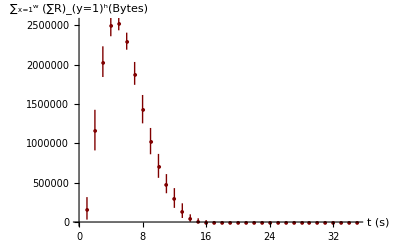
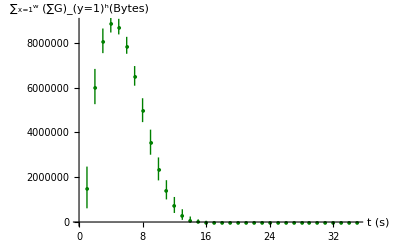
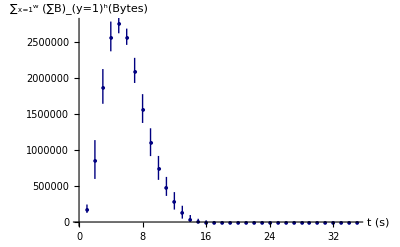
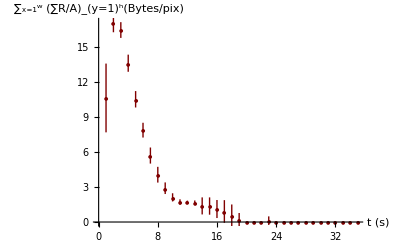
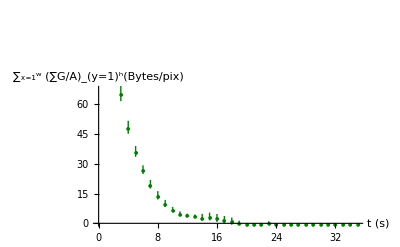
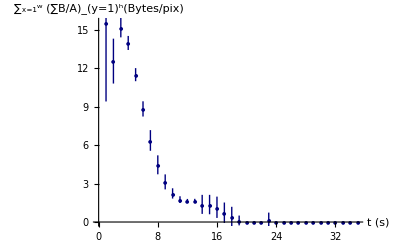

```mathematica
{redAAR6CC, greenAAR6CC, blueAAR6CC,cRedAAR6CC,cGreenAAR6CC,cBlueAAR6CC}=
{ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/2,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,1/2,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,0,1/2], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/2,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,1/2,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,0,1/2], PlotMarkers->{Automatic,5}]}
```

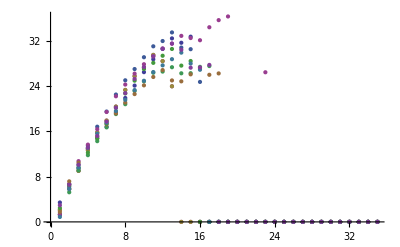
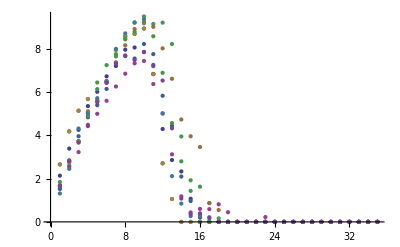
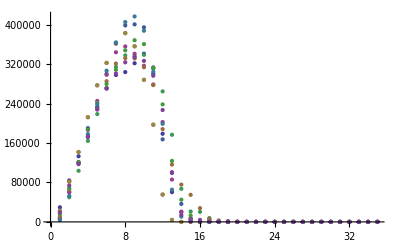
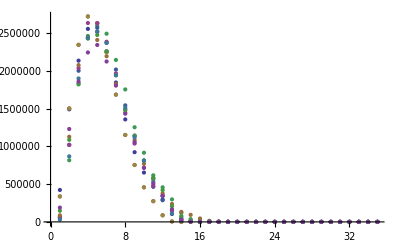
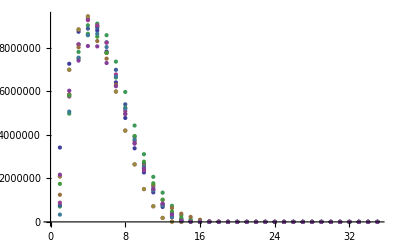
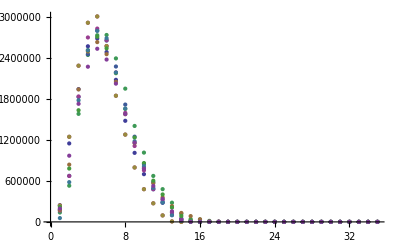
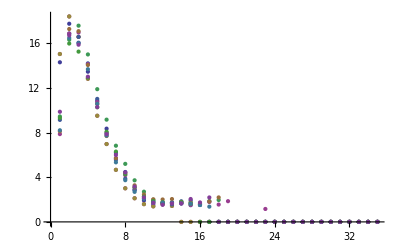
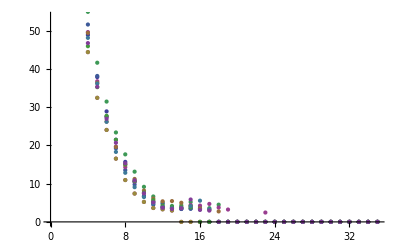

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

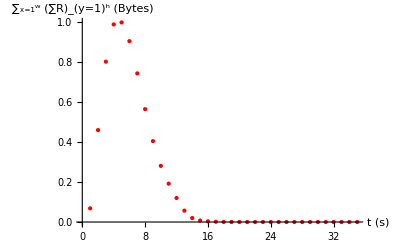
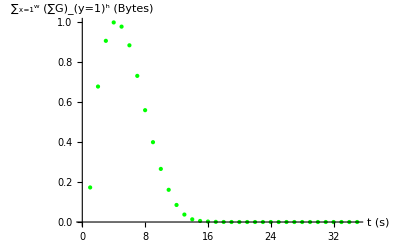
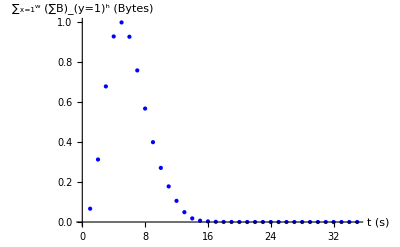

```mathematica
{ sclred, sclgreen, sclblue}=
{ErrorListPlot[ssclmtRedAll6, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[ssclmtGreenAll6, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[ssclmtBlueAll6, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```

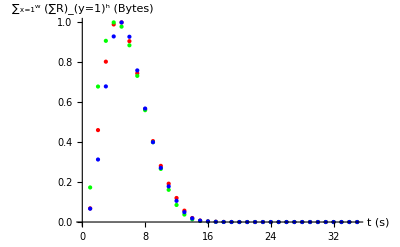

```mathematica
Show[sclred, sclgreen, sclblue]
```

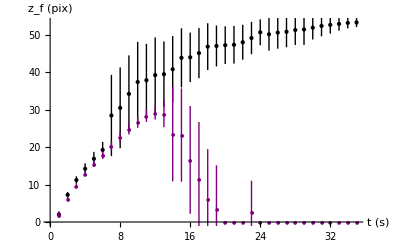

```mathematica
Show[{frontpositionAAI6,frontpositionAAR6},AxesOrigin->{0,0}]
```

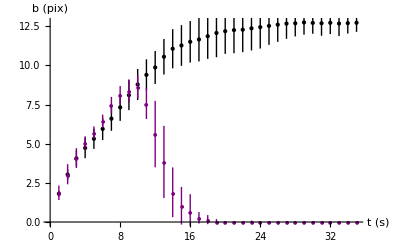

```mathematica
Show[{radiustAAI6,radiustAAR6},AxesOrigin->{0,0}]
```

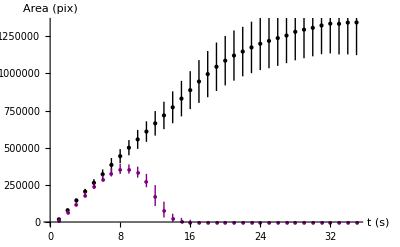

```mathematica
Show[{areaAAI6,areaAAR6},AxesOrigin->{0,0}]
```

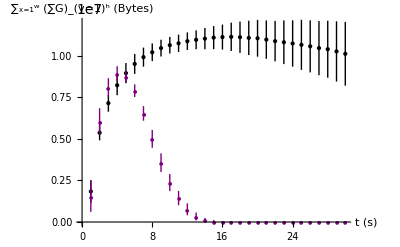

```mathematica
Show[{greenAAI6,greenAAR6},PlotRange->{{0,30},{0,12*10^6}},AxesOrigin->{0,0}]
```

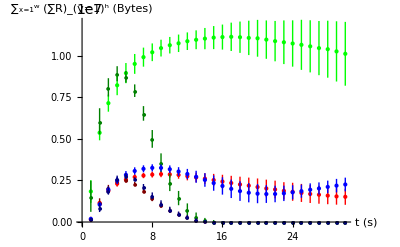

```mathematica
Show[ {redAAI6CC,redAAR6CC}, {greenAAI6CC,greenAAR6CC}, {blueAAI6CC,blueAAR6CC}, PlotRange->{{0,30},{0,12*10^6}}, AxesOrigin->{0,0}]
```

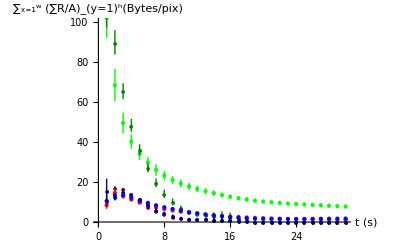

```mathematica
Show[ {cRedAAI6CC,cRedAAR6CC}, {cGreenAAI6CC,cGreenAAR6CC}, {cBlueAAI6CC,cBlueAAR6CC}, PlotRange->{{0,30},{0,100}}, AxesOrigin->{0,0}]
```

0.5M : Reactive

```mathematica
ntotal=10
```

10

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\0.5M\\"
SetDirectory[dir1];
```

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\0.5M\

```mathematica
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGB05M.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


(*If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];*)

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tGreenAll05=Max[mtGreenAll];
sclmtGreenAll05=mtGreenAll[[2;;15]]/tGreenAll05;

tGreenAll05=Max[mtGreenAll];
ssclmtGreenAll05=mtGreenAll/tGreenAll05;

tRedAll05=Max[mtRedAll];
ssclmtRedAll05=mtRedAll/tRedAll05;

tBlueAll05=Max[mtBlueAll];
ssclmtBlueAll05=mtBlueAll/tBlueAll05;

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]]
```

{8.75853,4.1264,0.294478,0.930435,0.182105,0.733532,0.893874,0.430421,0.,2.18197,0.,0.,0.,0.,0.}

```mathematica
Needs["ErrorBarPlots`"]
```

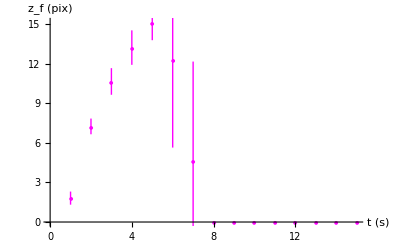
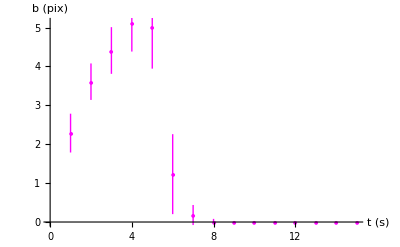
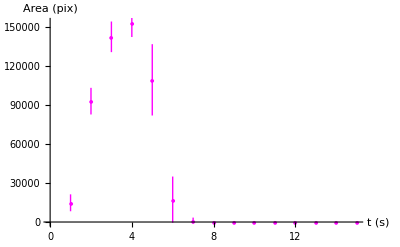
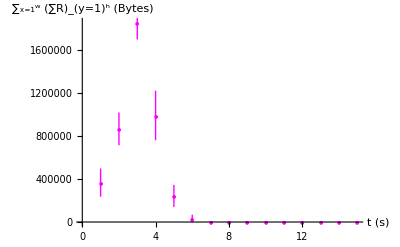
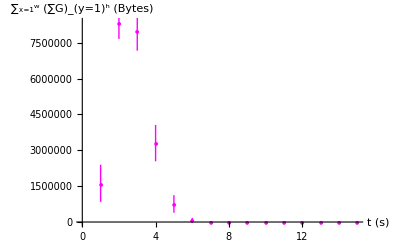
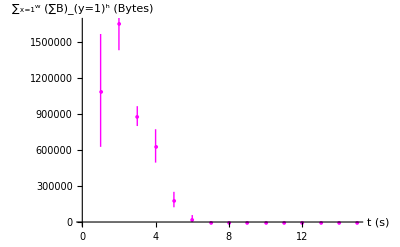
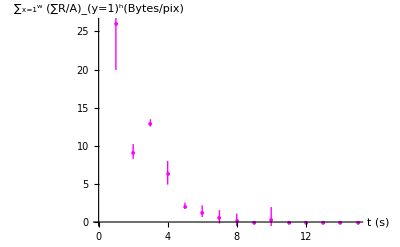
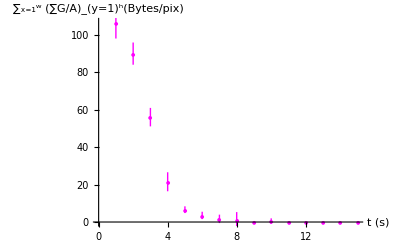

```mathematica
PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionAAR05, radiustAAR05, areaAAR05, redAAR05, greenAAR05, blueAAR05,cRedAAR05,cGreenAAR05,cBlueAAR05,sclgreenAAR05}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f (pix)"}, PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b (pix)"},  PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"},  PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"},  PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"},  PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"},  PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue,AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[sclmtGreenAll05, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/Max(G))_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1,0,1], PlotMarkers->{Automatic,5}]}
```

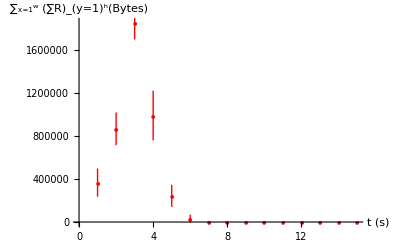
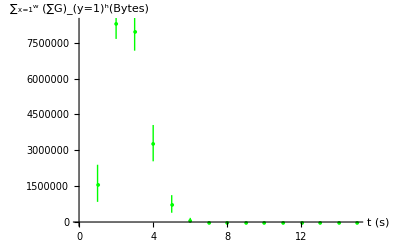
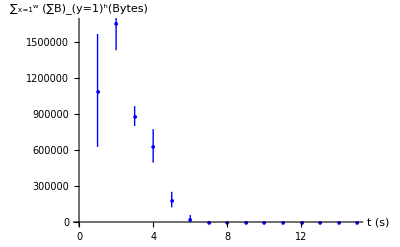
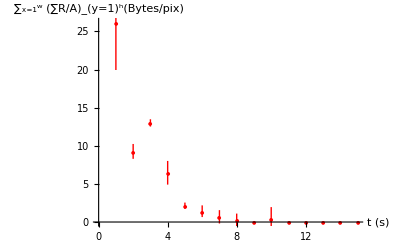
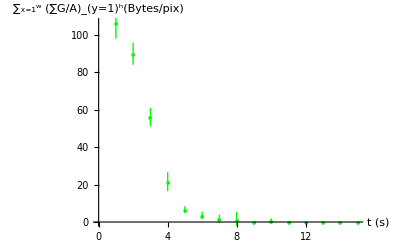
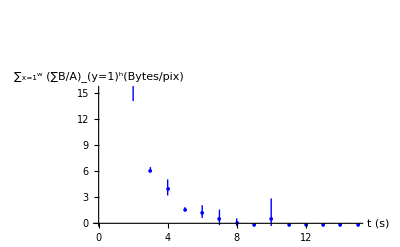

```mathematica
{redAAR05CC, greenAAR05CC, blueAAR05CC,cRedAAR05CC,cGreenAAR05CC,cBlueAAR05CC}=
{ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,1,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,0,1], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,1,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,0,1], PlotMarkers->{Automatic,5}]}
```

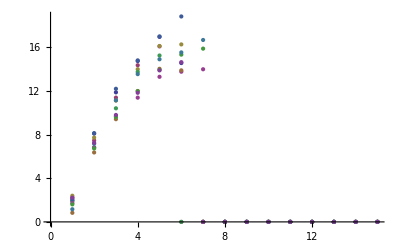
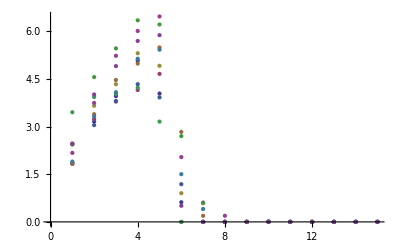
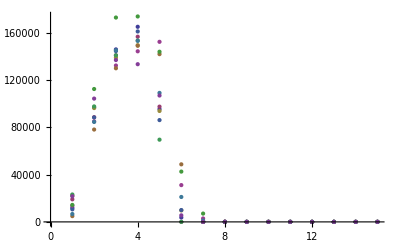
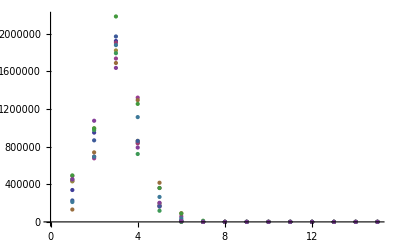
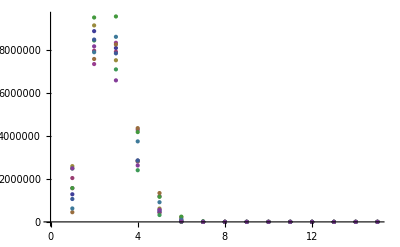
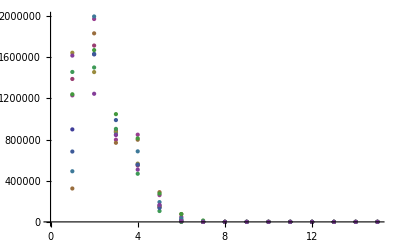
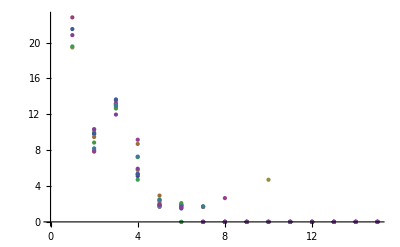
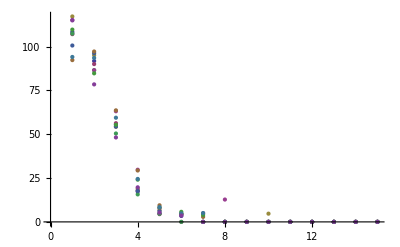

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

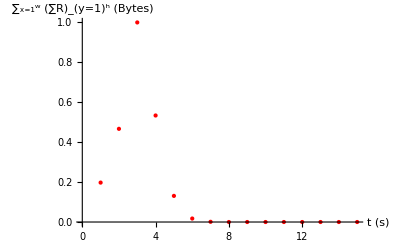
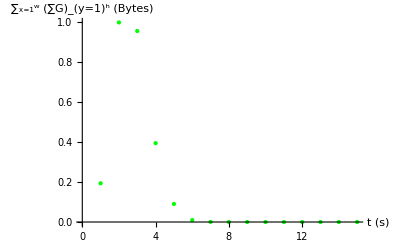
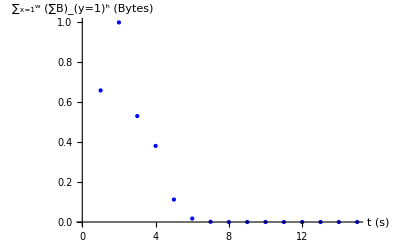

```mathematica
{ sclred, sclgreen, sclblue}=
{ErrorListPlot[ssclmtRedAll05, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[ssclmtGreenAll05, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[ssclmtBlueAll05, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```

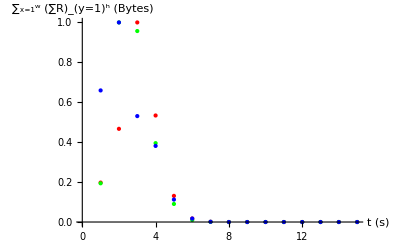

```mathematica
Show[sclred, sclgreen, sclblue]
```

2M : Reactive

```mathematica
ntotal=10
```

10

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\2M\

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_3\MB_3_AscA~0.05M\

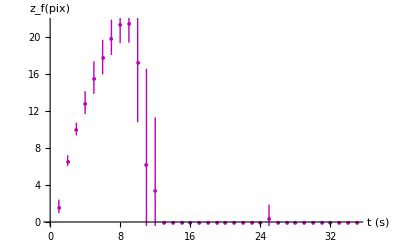
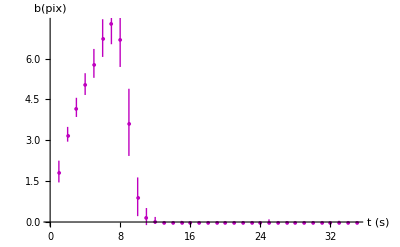
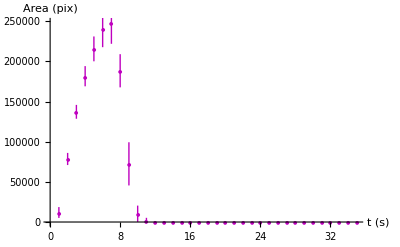
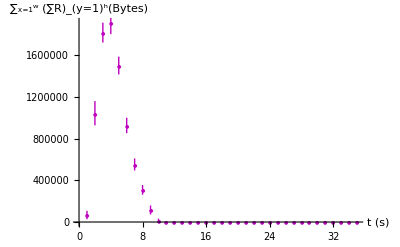
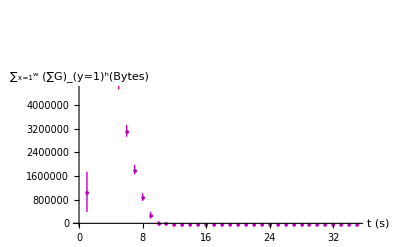
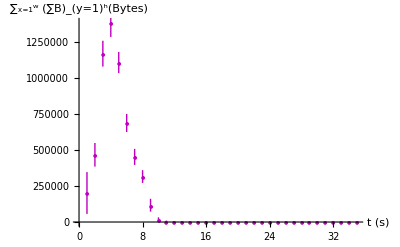
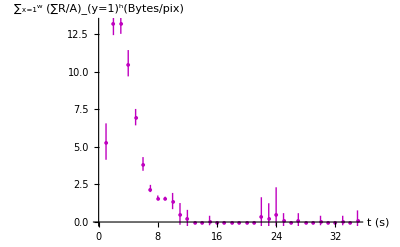
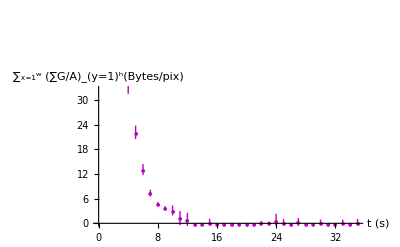

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\2M\\"
SetDirectory[dir1];
"C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_3\\MB_3_AscA~0.05M\\"
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGB2M.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


(*If[n<4,fp[n]=Join[fp[n],{0}];
b[n]=Join[b[n],{0}];
Area[n]=Join[Area[n],{0}];
tRed[n]=Join[tRed[n],{0}];
tGreen[n]=Join[tGreen[n],{0}];
tBlue[n]=Join[tBlue[n],{0}];

cRed[n]=Join[cRed[n],{0}];
cGreen[n]=Join[cGreen[n],{0}];
cBlue[n]=Join[cBlue[n],{0}];
];*)

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tGreenAll2=Max[mtGreenAll];
sclmtGreenAll2=mtGreenAll[[3;;35]]/tGreenAll2;

tGreenAll2=Max[mtGreenAll];
ssclmtGreenAll2=mtGreenAll/tGreenAll2;

tRedAll2=Max[mtRedAll];
ssclmtRedAll2=mtRedAll/tRedAll2;

tBlueAll2=Max[mtBlueAll];
ssclmtBlueAll2=mtBlueAll/tBlueAll2;

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]];

PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionAAR2, radiustAAR2, areaAAR2, redAAR2, greenAAR2, blueAAR2,cRedAAR2,cGreenAAR2,cBlueAAR2,sclgreenAAR2}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f(pix)"},  PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b(pix)"},PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"},PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"},PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[sclmtGreenAll2, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/Max(G))_(y=1)^h(Bytes/pix)"},PlotRange->{{0,35},{0,1}}, PlotStyle->RGBColor[3/4,0,3/4], PlotMarkers->{Automatic,5}]}
```

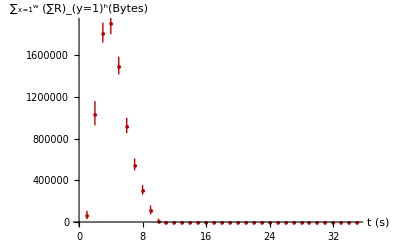
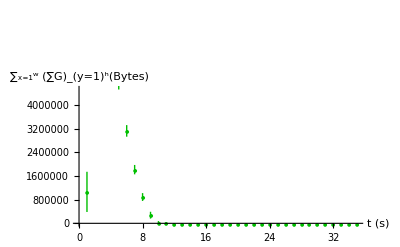
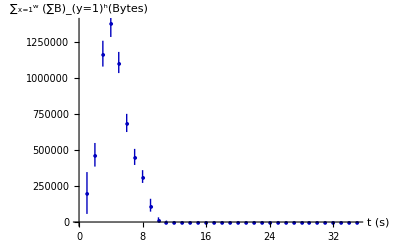
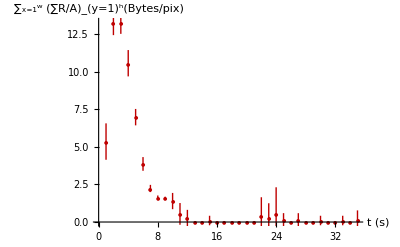
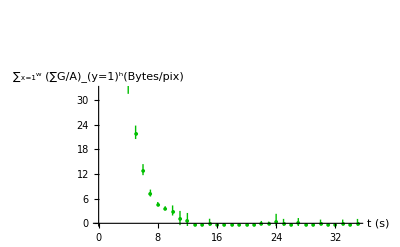
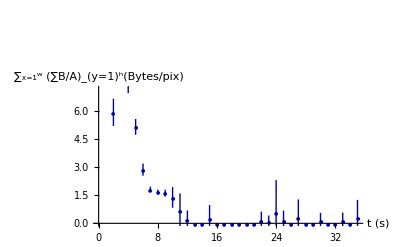

```mathematica
{redAAR2CC, greenAAR2CC, blueAAR2CC,cRedAAR2CC,cGreenAAR2CC,cBlueAAR2CC}=
{ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[3/4,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,3/4,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,0,3/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[3/4,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,3/4,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,0,3/4], PlotMarkers->{Automatic,5}]}
```

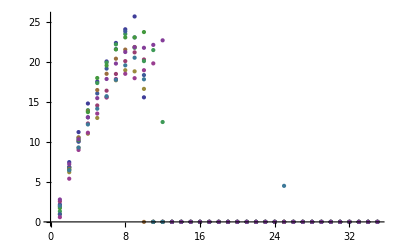
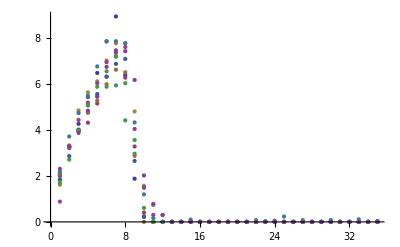
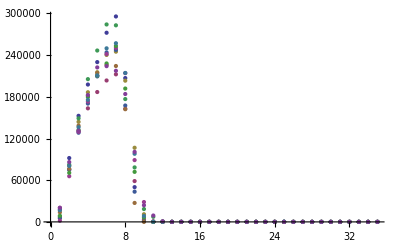
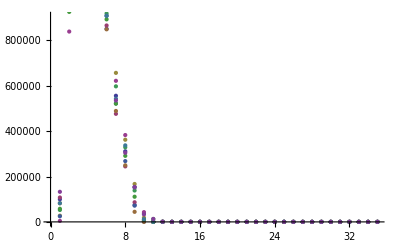
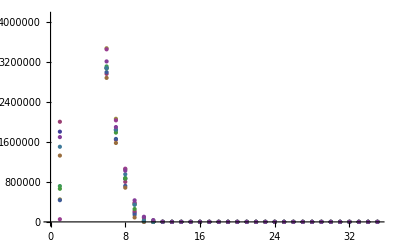
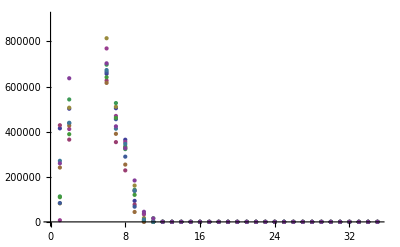
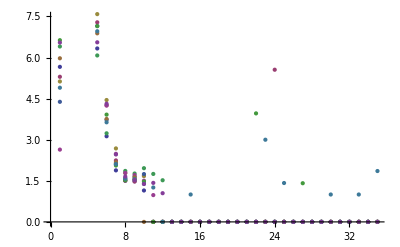
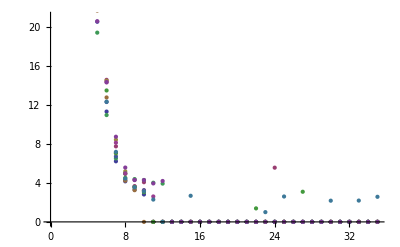

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

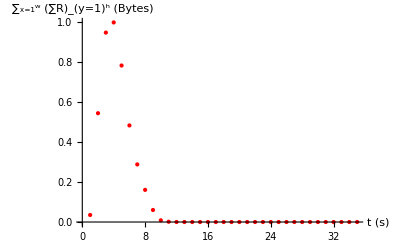
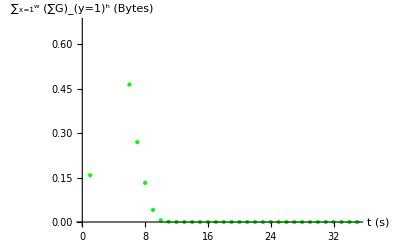
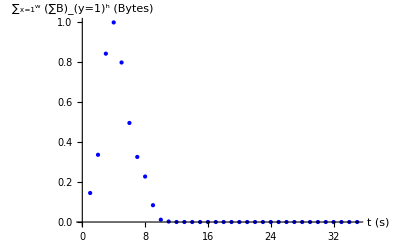

```mathematica
{ sclred, sclgreen, sclblue}=
{ErrorListPlot[ssclmtRedAll2, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[ssclmtGreenAll2, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[ssclmtBlueAll2, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```

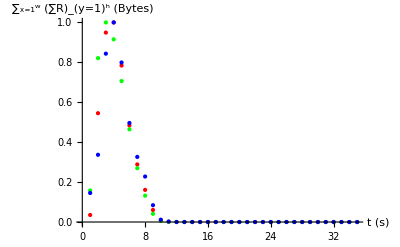

```mathematica
Show[sclred, sclgreen, sclblue]
```

9M : Reactive

```mathematica
ntotal=10
```

10

C:\Users\mariana\Desktop\LastPictures\Reactive\5%\9M\

C:\Users\mariana\Desktop\MBAA\AscA_MB\MB_3\MB_3_AscA~0.05M\

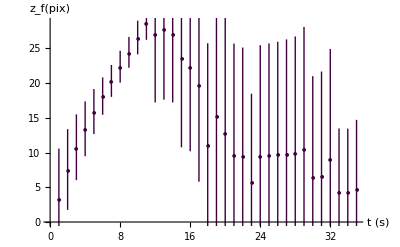
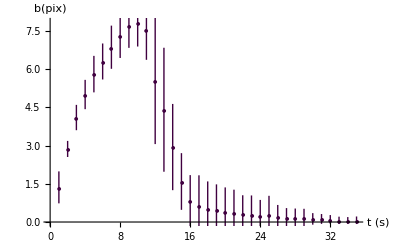
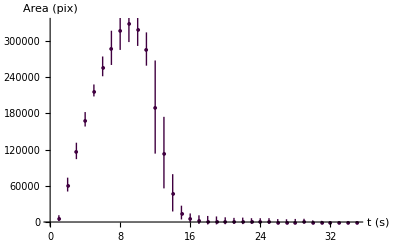
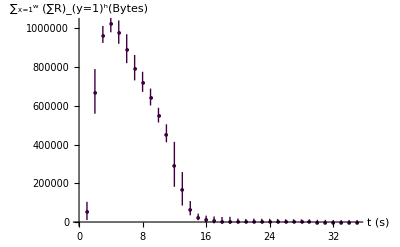
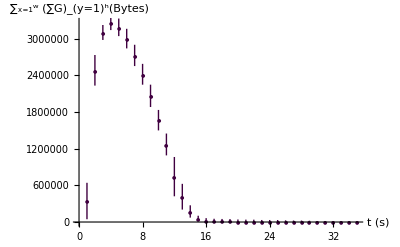
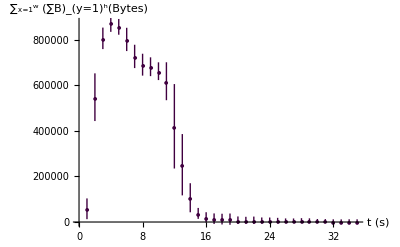
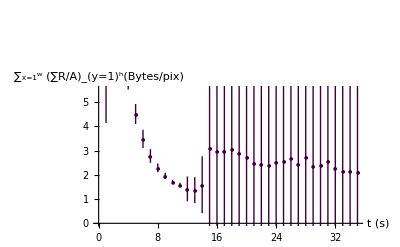
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
dir1="C:\\Users\\mariana\\Desktop\\LastPictures\\Reactive\\5%\\9M\\"
SetDirectory[dir1];
"C:\\Users\\mariana\\Desktop\\MBAA\\AscA_MB\\MB_3\\MB_3_AscA~0.05M\\"
For[n=1,n<ntotal+1,n=n+1,
m[n]=Import["dataRGB9M.xls"][[n]];
fp[n]=scl*m[n][[All,2]]/.{Null->0};
b[n]=scl*m[n][[All,3]]/.{Null->0};
Area[n]=m[n][[All,4]]/.{Null->0};
tRed[n]=m[n][[All,5]]/.{Null->0};
tGreen[n]=m[n][[All,6]]/.{Null->0};
tBlue[n]=m[n][[All,7]]/.{Null->0};

Areac[n]=Area[n]/.{0.->10^8};
cRed[n]=tRed[n]/Areac[n];
cGreen[n]=tGreen[n]/Areac[n];
cBlue[n]=tBlue[n]/Areac[n];


If[n>9,fp[n]=Join[fp[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
b[n]=Join[b[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
Area[n]=Join[Area[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
tRed[n]=Join[tRed[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
tGreen[n]=Join[tGreen[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
tBlue[n]=Join[tBlue[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];

cRed[n]=Join[cRed[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
cGreen[n]=Join[cGreen[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
cBlue[n]=Join[cBlue[n],{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}];
];

If[n>1,fpAll[n]=Join[{fpAll[n-1]},{fp[n]}];
bAll[n]=Join[{bAll[n-1]},{b[n]}];
AreaAll[n]=Join[{AreaAll[n-1]},{Area[n]}];
tRedAll[n]=Join[{tRedAll[n-1]},{tRed[n]}];
tGreenAll[n]=Join[{tGreenAll[n-1]},{tGreen[n]}];
tBlueAll[n]=Join[{tBlueAll[n-1]},{tBlue[n]}];

cRedAll[n]=Join[{cRedAll[n-1]},{cRed[n]}];
cGreenAll[n]=Join[{cGreenAll[n-1]},{cGreen[n]}];
cBlueAll[n]=Join[{cBlueAll[n-1]},{cBlue[n]}];

,
fpAll[n]=fp[n];
bAll[n]=b[n];
AreaAll[n]=Area[n];
tRedAll[n]=tRed[n];
tGreenAll[n]=tGreen[n];
tBlueAll[n]=tBlue[n];

cRedAll[n]=cRed[n];
cGreenAll[n]=cGreen[n];
cBlueAll[n]=cBlue[n];
];

If[n>2,fpAll[n]=Join[fpAll[n-1],{fp[n]}];
bAll[n]=Join[bAll[n-1],{b[n]}];
AreaAll[n]=Join[AreaAll[n-1],{Area[n]}];
tRedAll[n]=Join[tRedAll[n-1],{tRed[n]}];
tGreenAll[n]=Join[tGreenAll[n-1],{tGreen[n]}];
tBlueAll[n]=Join[tBlueAll[n-1],{tBlue[n]}];

cRedAll[n]=Join[cRedAll[n-1],{cRed[n]}];
cGreenAll[n]=Join[cGreenAll[n-1],{cGreen[n]}];
cBlueAll[n]=Join[cBlueAll[n-1],{cBlue[n]}]];

];


mfpAll=Mean[fpAll[ntotal]];
mbAll=Mean[bAll[ntotal]];
mAreaAll=Mean[AreaAll[ntotal]];
mtRedAll=Mean[tRedAll[ntotal]];
mtGreenAll=Mean[tGreenAll[ntotal]];
mtBlueAll=Mean[tBlueAll[ntotal]];

tGreenAll9=Max[mtGreenAll];
sclmtGreenAll9=mtGreenAll[[4;;35]]/tGreenAll9;

tGreenAll9=Max[mtGreenAll];
ssclmtGreenAll9=mtGreenAll/tGreenAll9;

tRedAll9=Max[mtRedAll];
ssclmtRedAll9=mtRedAll/tRedAll9;

tBlueAll9=Max[mtBlueAll];
ssclmtBlueAll9=mtBlueAll/tBlueAll9;

mcRedAll=Mean[cRedAll[ntotal]];
mcGreenAll=Mean[cGreenAll[ntotal]];
mcBlueAll=Mean[cBlueAll[ntotal]];


SDfpAll=StandardDeviation[fpAll[ntotal]];
SDbAll=StandardDeviation[bAll[ntotal]];
SDAreaAll=StandardDeviation[AreaAll[ntotal]];
SDtRedAll=StandardDeviation[tRedAll[ntotal]];
SDtGreenAll=StandardDeviation[tGreenAll[ntotal]];
SDtBlueAll=StandardDeviation[tBlueAll[ntotal]];

SDcRedAll=StandardDeviation[cRedAll[ntotal]];
SDcGreenAll=StandardDeviation[cGreenAll[ntotal]];
SDcBlueAll=StandardDeviation[cBlueAll[ntotal]];

PlotDatafp=Partition[Riffle[mfpAll,SDfpAll],2];
PlotDatab=Partition[Riffle[mbAll,SDbAll],2];
PlotDataArea=Partition[Riffle[mAreaAll,SDAreaAll],2];
PlotDatatRed=Partition[Riffle[mtRedAll,SDtRedAll],2];
PlotDatatGreen=Partition[Riffle[mtGreenAll,SDtGreenAll],2];
PlotDatatBlue=Partition[Riffle[mtBlueAll,SDtBlueAll],2];

PlotDatacRed=Partition[Riffle[mcRedAll,SDcRedAll],2];
PlotDatacGreen=Partition[Riffle[mcGreenAll,SDcGreenAll],2];
PlotDatacBlue=Partition[Riffle[mcBlueAll,SDcBlueAll],2];


{frontpositionAAR9, radiustAAR9, areaAAR9, redAAR9, greenAAR9, blueAAR9,cRedAAR9,cGreenAAR9,cBlueAAR9,sclgreenAAR9}=
{ErrorListPlot[PlotDatafp, AxesLabel->{"t (s)","z_f(pix)"},  PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatab, AxesLabel->{"t (s)","b(pix)"},PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDataArea, AxesLabel->{"t (s)","Area (pix)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"},PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"},PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[sclmtGreenAll9, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/Max(G))_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/4,0,1/4], PlotMarkers->{Automatic,5}]}
```

```mathematica
{redAAR9CC, greenAAR9CC, blueAAR9CC,cRedAAR9CC,cGreenAAR9CC,cBlueAAR9CC}=
{ErrorListPlot[PlotDatatRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[1/4,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,1/4,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatatBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h(Bytes)"}, PlotStyle->RGBColor[0,0,1/4], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacRed, AxesLabel->{"t (s)","∑_(x=1)^w (∑R/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[1/4,0,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacGreen, AxesLabel->{"t (s)","∑_(x=1)^w (∑G/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,1/4,0], PlotMarkers->{Automatic,5}],ErrorListPlot[PlotDatacBlue, AxesLabel->{"t (s)","∑_(x=1)^w (∑B/A)_(y=1)^h(Bytes/pix)"}, PlotStyle->RGBColor[0,0,1/4], PlotMarkers->{Automatic,5}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{frontposition, radiust, area, red, green, blue,cRedT,cGreenT,cBlueT}=
{ListPlot[fpAll[ntotal]],ListPlot[bAll[ntotal]],ListPlot[AreaAll[ntotal]],ListPlot[tRedAll[ntotal]],ListPlot[tGreenAll[ntotal]],ListPlot[tBlueAll[ntotal]],ListPlot[cRedAll[ntotal]],ListPlot[cGreenAll[ntotal]],ListPlot[cBlueAll[ntotal]]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{ sclred, sclgreen, sclblue}=
{ErrorListPlot[ssclmtRedAll9, AxesLabel->{"t (s)","∑_(x=1)^w (∑R)_(y=1)^h (Bytes)"}, PlotStyle->Red],ErrorListPlot[ssclmtGreenAll9, AxesLabel->{"t (s)","∑_(x=1)^w (∑G)_(y=1)^h (Bytes)"}, PlotStyle->Green],ErrorListPlot[ssclmtBlueAll9, AxesLabel->{"t (s)","∑_(x=1)^w (∑B)_(y=1)^h (Bytes)"}, PlotStyle->Blue]}
```

{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Show[sclred, sclgreen, sclblue]
```

-Graphics-

```mathematica
Show[{frontpositionAAR05,frontpositionAAR2,frontpositionAAR6,frontpositionAAR9},PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[{radiustAAR05,radiustAAR2,radiustAAR6,radiustAAR9},PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[{areaAAR05,areaAAR2,areaAAR6,areaAAR9},PlotRange->All,AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[{greenAAR05CC,greenAAR2CC,greenAAR6CC,greenAAR9CC},PlotRange->{{0,30},{0,10*10^6}},AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[{cGreenAAR05CC,cGreenAAR2CC,cGreenAAR6CC,cGreenAAR9CC},PlotRange->{{0,30},{0,10*10^1}},AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[ {redAAR05CC,redAAR2CC,redAAR6CC,redAAR9CC}, {greenAAR05CC,greenAAR2CC,greenAAR6CC,greenAAR9CC}, {blueAAR05CC,blueAAR2CC,blueAAR6CC,blueAAR9CC}, PlotRange->{{0,30},{0,10*10^6}}, AxesOrigin->{0,0}]
```

-Graphics-

```mathematica
Show[ {cRedAAR05CC,cRedAAR2CC,cRedAAR6CC,cRedAAR9CC}, {cGreenAAR05CC,cGreenAAR2CC,cGreenAAR6CC,cGreenAAR9CC}, {cBlueAAR05CC,cBlueAAR2CC,cBlueAAR6CC,cBlueAAR9CC}, PlotRange->{{0,30},{0,100}}, AxesOrigin->{0,0}]
```

-Graphics-

# Theory/Experiments : Acetic Acid - Ammonia System

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=0.5*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=10^8*10^6;
```

```mathematica
Grxn=12843.25;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0^(-1)*na[t])/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

```mathematica
{g105,g205,g305,g405,g505,g605,g705,g805, g905, g1005}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

3.9654

```mathematica
zex[azero]
```

13.1127

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=2*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=10^8*10^6;
```

```mathematica
Grxn=12843.25;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0^(-1)*na[t])/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

```mathematica
{g12,g22,g32,g42,g52,g62,g72,g82, g92, g102}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

4.59761

```mathematica
zex[azero]
```

14.593

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=6*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=10^8*10^6;
```

```mathematica
Grxn=12843.25;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=30
```

30

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,30.}},<>],m→InterpolatingFunction[{{0.0001,30.}},<>],b→InterpolatingFunction[{{0.0001,30.}},<>],na→InterpolatingFunction[{{0.0001,30.}},<>],nb→InterpolatingFunction[{{0.0001,30.}},<>],height→InterpolatingFunction[{{0.0001,30.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0^(-1)*na[t])/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

```mathematica
{g16,g26,g36,g46,g56,g66,g76,g86, g96, g106}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,4}]
```

10.7197

```mathematica
zex[azero]
```

26.1018

```mathematica
(*Geometrical parameters considering a completely spherical thermal*)
```

```mathematica
s=4*Pi;
```

```mathematica
mg=4/3*Pi;
```

```mathematica
c=1;
```

```mathematica
(*entrainment coefficient*)
```

```mathematica
alpha=0.25;
```

```mathematica
n=3*mg/(s*alpha);
```

```mathematica
(*added mass coefficient*)
```

```mathematica
k=0;
```

```mathematica
(*bc/bw, ratio of the concentration and volume radius*)
```

```mathematica
lambda=0.7;
```

```mathematica
(*Experimental conditions*)
```

```mathematica
v0=10;
```

```mathematica
v430=v0^(4/3);
```

```mathematica
m0=0.00000001;
```

```mathematica
b0=10*981*(1.05-1)/1;
```

```mathematica
Cbinf=0.05*10^(-3);
```

```mathematica
CA0=9*10^(-3);
```

```mathematica
na0=CA0*v0;
```

```mathematica
nb0=0;
```

```mathematica
z0=0;
```

```mathematica
(*Reaction conditions*)
```

```mathematica
kr=10^8*10^6;
```

```mathematica
Grxn=12843.25;
```

```mathematica
(*Environmental conditions*)
```

```mathematica
N2=0;
```

```mathematica
tmax=14
```

14

```mathematica
system={v43'[t]==4/3*s*alpha/(mg^(2/3)*(1+k)*(1-c/n))*Abs[m[t]],m'[t]==b[t],b'[t]==-N2/(1+k)*m[t]+Grxn*kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),na'[t]==-kr*na[t]*Abs[nb[t]]/(v43[t]^(3/4)*lambda^3),nb'[t]==lambda^3*(v43[t]^(-1/4))*s*alpha*Abs[m[t]]*Cbinf/(mg^(2/3)*(1+k)*(1-c/n))-kr*na[t]*nb[t]/(v43[t]^(3/4)*lambda^3),height'[t]==lambda*m[t]/(v43[t]^(3/4)*(1+k)*(1-c/n)),v43[0.]==v430,m[0.]==m0,b[0.]==b0,na[0.]==na0,nb[0.]==nb0,height[0.]==z0};
```

```mathematica
sol1=NDSolve[system,{v43,m,b,na,nb,height},{t,0.0001,tmax}]
```

{{v43→InterpolatingFunction[{{0.0001,14.}},<>],m→InterpolatingFunction[{{0.0001,14.}},<>],b→InterpolatingFunction[{{0.0001,14.}},<>],na→InterpolatingFunction[{{0.0001,14.}},<>],nb→InterpolatingFunction[{{0.0001,14.}},<>],height→InterpolatingFunction[{{0.0001,14.}},<>]}}

```mathematica
clear[v4ex,mex,bex,maex,zex];
```

```mathematica
v43ex[t_]=v43[t]/.sol1[[1,1]];
```

```mathematica
mex[t_]=m[t]/.sol1[[1,2]];
```

```mathematica
bex[t_]=b[t]/.sol1[[1,3]];
```

```mathematica
naex[t_]=(na0^(-1)*na[t])/.sol1[[1,4]];
```

```mathematica
nbex[t_]=nb[t]/.sol1[[1,5]];
```

```mathematica
zex[t_]=height[t]/.sol1[[1,6]];
```

```mathematica
vex[t_]=v43ex[t]^(3/4);
```

```mathematica
velocity[t_]=mex[t]/(v43ex[t]*(1+k)*(1-c/n));
```

```mathematica
radius[t_]=lambda*vex[t]^(1/3);
```

```mathematica
ca[t_]=naex[t]/vex[t];
cb[t_]=nbex[t]/vex[t];
```

```mathematica
{g19,g29,g39,g49,g59,g69,g79,g89, g99, g109}={Plot[Evaluate[{vex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","V (mL)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{mex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","M (cm4/s)"}, PlotStyle->{GrayLevel[0.]}], Plot[Evaluate[{bex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","B (cm4/s2)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{naex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","NA (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{nbex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","Nb (mol)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{velocity[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","w (cm/s)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{radius[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","b (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{zex[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All,AxesLabel->{"t(s)","z (cm)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{ca[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","ca (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}],Plot[Evaluate[{cb[t]}],{t,0.,tmax}, AxesOrigin->{0,0},PlotRange->All, AxesLabel->{"t","cb (mol/cm3)"}, PlotStyle->{GrayLevel[0.]}]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
azero= t/.FindRoot[naex[t]==0,{t,13}]
```

InterpolatingFunction::dmval: Input value {14.1336} lies outside the range of data in the interpolating function. Extrapolation will be used.

13.0854

```mathematica
zex[azero]
```

30.2404

```mathematica
{Jntfp05,Jntfp2,Jntfp6,Jntfp9}={Show[g805,frontpositionAAR05],Show[g82,frontpositionAAR2],Show[g86,frontpositionAAR6],Show[g89,frontpositionAAR9]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Jntradius05,Jntradius2,Jntradius6,Jntradius9}={Show[g705,radiustAAR05],Show[g72,radiustAAR2],Show[g76,radiustAAR6],Show[g79,radiustAAR9]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Jntgreen05,Jntgreen2,Jntgreen6,Jntgreen9}={Show[g405,sclgreenAAR05],Show[g42,sclgreenAAR2],Show[g46,sclgreenAAR6],Show[g49,sclgreenAAR9]}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{JntgreenT,JntgreenExp}={Show[g405,g42,g46,g49],Show[sclgreenAAR05,sclgreenAAR2,sclgreenAAR6,sclgreenAAR9]}
```

{-Graphics-,-Graphics-}